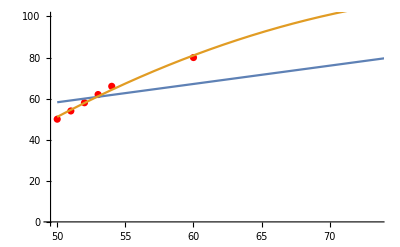

```mathematica
data={{50,50},{51,54},{52,58},{53,62}, {54, 66}, {60, 80}, {100, 100}};
model=a Exp[k x];
DesignMatrix[data,{1,x},x];
line=Fit[data,{1,x},x];
parabola=Fit[data,{1,x,x^2},x];
Show[ListPlot[data,PlotStyle->Red],Plot[{line,parabola},{x,50,100}]]
```

```mathematica
Fit[data,{1,x,x^2},x];
```

```mathematica
-249.89749898363678+8.54126545054616 x-0.050425690982083646 x^2
```

-249.897+8.54127 x-0.0504257 x^2

```mathematica
FullSimplify[-249.89749898363678+8.54126545054616 x-0.050425690982083646 x^2]
```

-249.897+(8.54127-0.0504257 x) x

```mathematica
-249.89749898363678+8.54126545054616 x-0.050425690982083646 x^2
```

-249.897+8.54127 x-0.0504257 x^2

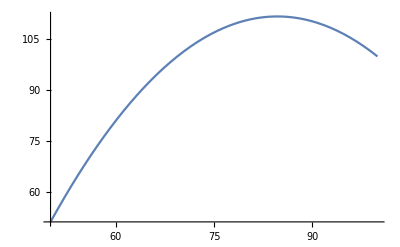

```mathematica
Plot[-249.89749898363678+8.54126545054616 x-0.050425690982083646 x^2, {x, 50, 100}]
```

```mathematica
fit = FindFit[data, model, {a, k}, t]
```

{a→3.72008×10^-42,k→1.}

```mathematica
modelf=Function[{t},Evaluate[model/.fit]]
```

Function[{t},3.72008×10^-42 ⅇ^(1. t)]

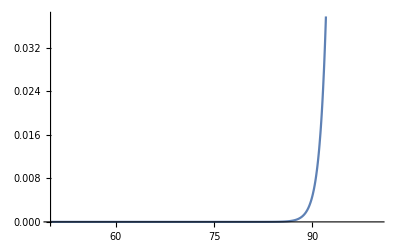

```mathematica
Plot[modelf[t],{t,50,100},Epilog->Map[Point,data]]
```

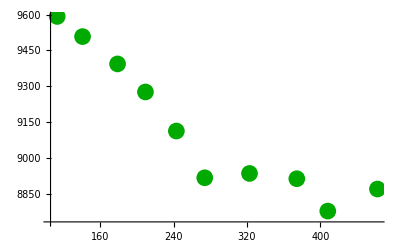

```mathematica
data2={{462.36,8872},{408.18,8780},{374.4,8915},{322.8,8937},{274.00,8919},{243.03,9114},{209.32,9277},{178.91,9394},{140.71,9508},{113.08,9592}};
nlm=NonlinearModelFit[data,a+b Exp[-x/c],{{a,100},{b,100},{c,10}},x];
Show[ListPlot[data,PlotStyle->{Darker@Green,PointSize[0.03]}],Plot[nlm[x],{x,50,100}]]
```

FittedModel[100.487-4965.35 ⅇ^(-0.0917014 x)]

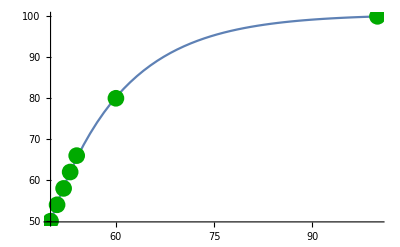

```mathematica
data={{50,50},{51,54},{52,58},{53,62}, {54, 66}, {60, 80}, {100, 100}};
nlm=NonlinearModelFit[data,a+b Exp[-x/c],{{a, 100},{b, 100},{c, 10}},x]
Show[Plot[nlm[x],{x,50,100}],ListPlot[data,PlotStyle->{Darker@Green,PointSize[0.03]}]]
```

```mathematica
data={{50,50},{51,54},{52,58},{53,62}, {54, 66}, {60, 80}, {100, 100}};
nlm=NonlinearModelFit[data,a+b Exp[-x/c],{{a, 100},{b, 100},{c, 10}},x];
```

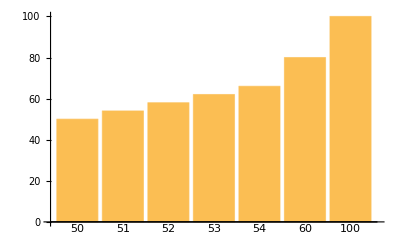

```mathematica
BarChart[Apply[Labeled,Reverse[{{50,50},{51,54},{52,58},{53,62},{54,66},{60,80},{100,100}},2],{1}]]
```

```mathematica
100.48657973609443-4965.346815032645 ⅇ^(-0.09170141305689222 x)
```

100.487-4965.35 ⅇ^(-0.0917014 x)

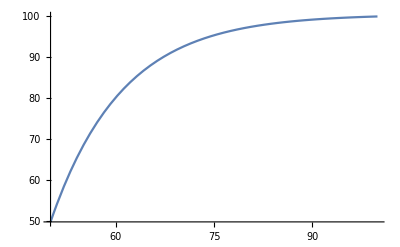

```mathematica
Plot[100.48657973609443-4965.346815032645 ⅇ^(-0.09170141305689222 x),{x,50, 100}]
```